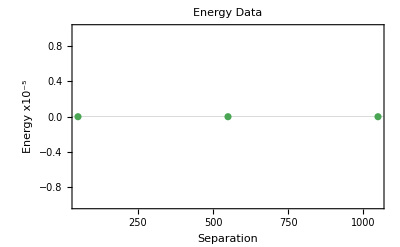

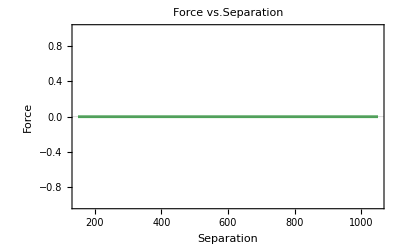

-Graphics-

-Graphics-

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/SpeedTest/gpls/positive"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]

files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString];
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)

SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/SpeedTest/gpls/negative"];
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString];
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)

SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];

SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/SpeedTest"];
(*Print[SolveForce["energysep.txt"]];*)
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}];
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]];
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}];
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];

SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/SpeedTest"];
(*Print[SolveForce["energysep2.txt"]];*)
allData2=SolveForce["energysep2.txt"];
{sep2, energy2}= Transpose[allData2];
showData2 = Transpose[{sep2,Map[#/(10^5)&,energy2//N]}];
energyGraph2 = ListPlot[showData2, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]];
(*ListPlot[allData,Joined->True]*)
force2[x_]=-D[Interpolation[allData2,InterpolationOrder->1][x],x];
forceGraph2 = Plot[force2[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}];
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];

energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full,  PlotRange->All]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full, PlotRange->All]

energyGraphnice2 = Show[energyGraph2,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full,  PlotRange->All]
forceGraphnice2 = Show[forceGraph2,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full, PlotRange->All]
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/SpeedTest/gpls/positive"];
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2,minz,maxz},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
minz=Min[Transpose[data][[3]]];
maxz=Max[Transpose[data][[3]]];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->All(*{minz,maxz}*),RegionFunction->Function[{x,y,z},x^2+y^2>100-0.01]];
prettyData
]
prettySurface["surface0positive.gpl"]
Show[prettySurface["surface0positive.gpl"],Axes->True,AxesStyle->Black,ViewPoint->Front]
```

-Graphics3D-

-Graphics3D-

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.